# 9

## PHAS2443: Practical Mathematics II Lecture 9: Integral transforms and Fourier methods

## Introduction

As we know, there are many functions that are defined as expansions in powers of x. First, let us work through a problem in mathematical notation, then do the same problem in Mathematica, making the Mathematica version look as much like conventional mathematics as possible.
If we think of the various powers of x as a set of basis functions,
     b_n(x)=x^n, 
 the expansion of a function f(x) is written as
     f(x) = ∑_(n =0)^∞ a_n x^n =∑_(n =0)^∞ a_n b_n(x) .
There is nothing special about the simple powers: the basis functions could take any form. Now suppose we multiply this expansion equation by one of the other basis functions and integrate (the integration will be over the whole range of x under consideration, so every integral will yield just a number, and we assume that there are no problems with the convergence of the integrals. Then
    ∫ b_m(x)f(x) dx =∫  ∑_(n =0)^∞ a_n b_m(x) b_n(x) dx
                                   = ∑_(n =0)^∞ a_n ∫b_m(x) b_n(x) dx
or, if we define
  v_m=∫b_m(x)f(x) dx,
and
  S_(m,n) =∫b_m(x) b_n(x) dx,
then
   v_m= ∑_(n =0)^∞ S_(m,n)a_n 
which we could write in vector notation as
  v = S a,
with a formal solution
  a = S^-1 v,
glossing over the fact that the matrix has infinite order, we have a means of finding the unknown coefficients a_n.
In Mathematica notation, with basis functions
    b[n][x]=x^n,
    the expansion of a function f[x] is written as

```mathematica
f[x]==∑_(n=0)^∞ a[n] b[n][x]
```

f[x]==∑_(n=0)^∞ a[n] b[n][x]

and ideally we would like to see this displayed as

f[x]==∑_(n=0)^∞ a_n b_n[x]

To get the results displayed in this more familiar mathematical notation, we force a subscript style onto a and b when they are printed:

```mathematica
Format[a[n_]]:=Subscripted[a[n]]
Format[b[n_][x_]]:=Subscripted[b[n]][x]
```

```mathematica
FormatValues[a]
```

{HoldPattern[MakeBoxes[a_n_,FormatType_]]:>Format[a_n,FormatType],HoldPattern[a_n_]:>a_n}

Let us take a finite-length expansion to illustrate a point

```mathematica
maxpow=3
exp=f[x]==∑_(n=0)^maxpow a[n] b[n][x]
```

3

f[x]==a_0 b_0[x]+a_1 b_1[x]+a_2 b_2[x]+a_3 b_3[x]

now multiply by b[m] and integrate over the range of interest, -1 to 1 say

```mathematica
vex=Map[Expand,Thread[b[m][x] #&[exp],Equal]]
```

f[x] b_m[x]==a_0 b_0[x] b_m[x]+a_1 b_1[x] b_m[x]+a_2 b_2[x] b_m[x]+a_3 b_3[x] b_m[x]

We needed to Map Expand onto the expression in order to force Mathematica to expand both sides of the equation.

```mathematica
v[m]=Thread[∫_-1^1  # ⅆx&[vex],Equal]//.∫_-1^1 (a_+b_)ⅆx:>∫_-1^1 aⅆx+∫_-1^1 bⅆx
```

∫_-1^1 f[x] b_m[x]ⅆx==∫_-1^1 a_0 b_0[x] b_m[x]ⅆx+∫_-1^1 a_1 b_1[x] b_m[x]ⅆx+∫_-1^1 a_2 b_2[x] b_m[x]ⅆx+∫_-1^1 a_3 b_3[x] b_m[x]ⅆx

Now the coefficients a_i are independent of x. Suppose the integral of b[i] b[j] is s[i,j] and that the integral of b[i] f  is ϕ[i], then, again using subscript notation,

```mathematica
Format[s[i_,j_]]:=Subscripted[s[i,j]]
Format[ϕ[i_]]:=Subscripted[ϕ[i]]
```

```mathematica
vv[m_]=v[m]/.∫_-1^1 q_ b[i_][x]b[j_][x]ⅆx->q s[i,j]/.∫_-1^1 q_ b[i_][x] f[x]ⅆx->q ϕ[i]
```

∫_-1^1 f[x] b_m[x]ⅆx==a_0 s_(0,m)+a_1 s_(1,m)+a_2 s_(2,m)+a_3 s_(3,m)

There will be one such equation for each value of m, so we may group these together to form a set of simultaneous equations for the a coefficients.

```mathematica
seq=Table[vv[m],{m,0,maxpow}]
```

{∫_-1^1 f[x] b_0[x]ⅆx==a_0 s_(0,0)+a_1 s_(1,0)+a_2 s_(2,0)+a_3 s_(3,0),∫_-1^1 f[x] b_1[x]ⅆx==a_0 s_(0,1)+a_1 s_(1,1)+a_2 s_(2,1)+a_3 s_(3,1),∫_-1^1 f[x] b_2[x]ⅆx==a_0 s_(0,2)+a_1 s_(1,2)+a_2 s_(2,2)+a_3 s_(3,2),∫_-1^1 f[x] b_3[x]ⅆx==a_0 s_(0,3)+a_1 s_(1,3)+a_2 s_(2,3)+a_3 s_(3,3)}

In principle, we can use Solve to evaluate this -- but the resulting expressions are enormous and not very easy to work with.

```mathematica
sol=Solve[seq,Table[a[i],{i,0,maxpow}]]//Simplify
```

{{a_0→-((-((∫_-1^1 f[x] b_2[x]ⅆx) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+(∫_-1^1 f[x] b_1[x]ⅆx) (s_(2,2) s_(3,0)-s_(2,0) s_(3,2))+(∫_-1^1 f[x] b_0[x]ⅆx) (-s_(2,2) s_(3,1)+s_(2,1) s_(3,2))) (s_(1,3) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,3) s_(3,0)+s_(2,0) s_(3,3))+s_(1,0) (s_(2,3) s_(3,1)-s_(2,1) s_(3,3)))+(s_(1,2) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,2) s_(3,0)+s_(2,0) s_(3,2))+s_(1,0) (s_(2,2) s_(3,1)-s_(2,1) s_(3,2))) ((∫_-1^1 f[x] b_3[x]ⅆx) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+(∫_-1^1 f[x] b_1[x]ⅆx) (s_(2,3) s_(3,0)-s_(2,0) s_(3,3))+(∫_-1^1 f[x] b_0[x]ⅆx) (-s_(2,3) s_(3,1)+s_(2,1) s_(3,3))))/((s_(1,2) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,2) s_(3,0)+s_(2,0) s_(3,2))+s_(1,0) (s_(2,2) s_(3,1)-s_(2,1) s_(3,2))) (s_(0,3) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(0,1) (-s_(2,3) s_(3,0)+s_(2,0) s_(3,3))+s_(0,0) (s_(2,3) s_(3,1)-s_(2,1) s_(3,3)))-(s_(0,2) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(0,1) (-s_(2,2) s_(3,0)+s_(2,0) s_(3,2))+s_(0,0) (s_(2,2) s_(3,1)-s_(2,1) s_(3,2))) (s_(1,3) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,3) s_(3,0)+s_(2,0) s_(3,3))+s_(1,0) (s_(2,3) s_(3,1)-s_(2,1) s_(3,3))))),a_1→((∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(2,2) s_(3,0)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(2,3) s_(3,0)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(2,2) s_(3,1)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(2,3) s_(3,1)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(2,0) s_(3,2)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(2,1) s_(3,2)+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(2,3) s_(3,2)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(2,3) s_(3,2)+(∫_-1^1 f[x] b_3[x]ⅆx) (s_(0,2) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(0,1) (-s_(2,2) s_(3,0)+s_(2,0) s_(3,2))+s_(0,0) (s_(2,2) s_(3,1)-s_(2,1) s_(3,2)))+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(2,0) s_(3,3)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(2,1) s_(3,3)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(2,2) s_(3,3)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(2,2) s_(3,3)+(∫_-1^1 f[x] b_2[x]ⅆx) (s_(0,3) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+s_(0,1) (s_(2,3) s_(3,0)-s_(2,0) s_(3,3))+s_(0,0) (-s_(2,3) s_(3,1)+s_(2,1) s_(3,3))))/(-s_(0,1) s_(1,3) s_(2,2) s_(3,0)+s_(0,1) s_(1,2) s_(2,3) s_(3,0)+s_(0,0) s_(1,3) s_(2,2) s_(3,1)-s_(0,0) s_(1,2) s_(2,3) s_(3,1)+s_(0,1) s_(1,3) s_(2,0) s_(3,2)-s_(0,0) s_(1,3) s_(2,1) s_(3,2)-s_(0,1) s_(1,0) s_(2,3) s_(3,2)+s_(0,0) s_(1,1) s_(2,3) s_(3,2)+s_(0,3) (s_(1,2) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+s_(1,1) (s_(2,2) s_(3,0)-s_(2,0) s_(3,2))+s_(1,0) (-s_(2,2) s_(3,1)+s_(2,1) s_(3,2)))-s_(0,1) s_(1,2) s_(2,0) s_(3,3)+s_(0,0) s_(1,2) s_(2,1) s_(3,3)+s_(0,1) s_(1,0) s_(2,2) s_(3,3)-s_(0,0) s_(1,1) s_(2,2) s_(3,3)+s_(0,2) (s_(1,3) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,3) s_(3,0)+s_(2,0) s_(3,3))+s_(1,0) (s_(2,3) s_(3,1)-s_(2,1) s_(3,3)))),a_2→((∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(1,2) s_(3,0)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(1,3) s_(3,0)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(1,2) s_(3,1)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(1,3) s_(3,1)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(1,0) s_(3,2)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(1,1) s_(3,2)+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(1,3) s_(3,2)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(1,3) s_(3,2)+(∫_-1^1 f[x] b_3[x]ⅆx) (s_(0,2) (s_(1,1) s_(3,0)-s_(1,0) s_(3,1))+s_(0,1) (-s_(1,2) s_(3,0)+s_(1,0) s_(3,2))+s_(0,0) (s_(1,2) s_(3,1)-s_(1,1) s_(3,2)))+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(1,0) s_(3,3)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(1,1) s_(3,3)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(1,2) s_(3,3)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(1,2) s_(3,3)+(∫_-1^1 f[x] b_2[x]ⅆx) (s_(0,3) (-s_(1,1) s_(3,0)+s_(1,0) s_(3,1))+s_(0,1) (s_(1,3) s_(3,0)-s_(1,0) s_(3,3))+s_(0,0) (-s_(1,3) s_(3,1)+s_(1,1) s_(3,3))))/(s_(0,1) s_(1,3) s_(2,2) s_(3,0)-s_(0,1) s_(1,2) s_(2,3) s_(3,0)-s_(0,0) s_(1,3) s_(2,2) s_(3,1)+s_(0,0) s_(1,2) s_(2,3) s_(3,1)-s_(0,1) s_(1,3) s_(2,0) s_(3,2)+s_(0,0) s_(1,3) s_(2,1) s_(3,2)+s_(0,1) s_(1,0) s_(2,3) s_(3,2)-s_(0,0) s_(1,1) s_(2,3) s_(3,2)+s_(0,3) (s_(1,2) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,2) s_(3,0)+s_(2,0) s_(3,2))+s_(1,0) (s_(2,2) s_(3,1)-s_(2,1) s_(3,2)))+s_(0,1) s_(1,2) s_(2,0) s_(3,3)-s_(0,0) s_(1,2) s_(2,1) s_(3,3)-s_(0,1) s_(1,0) s_(2,2) s_(3,3)+s_(0,0) s_(1,1) s_(2,2) s_(3,3)+s_(0,2) (s_(1,3) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+s_(1,1) (s_(2,3) s_(3,0)-s_(2,0) s_(3,3))+s_(1,0) (-s_(2,3) s_(3,1)+s_(2,1) s_(3,3)))),a_3→((∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(1,2) s_(2,0)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(1,3) s_(2,0)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(1,2) s_(2,1)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(1,3) s_(2,1)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,3) s_(1,0) s_(2,2)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,3) s_(1,1) s_(2,2)+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(1,3) s_(2,2)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(1,3) s_(2,2)+(∫_-1^1 f[x] b_3[x]ⅆx) (s_(0,2) (s_(1,1) s_(2,0)-s_(1,0) s_(2,1))+s_(0,1) (-s_(1,2) s_(2,0)+s_(1,0) s_(2,2))+s_(0,0) (s_(1,2) s_(2,1)-s_(1,1) s_(2,2)))+(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,2) s_(1,0) s_(2,3)-(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,2) s_(1,1) s_(2,3)-(∫_-1^1 f[x] b_1[x]ⅆx) s_(0,0) s_(1,2) s_(2,3)+(∫_-1^1 f[x] b_0[x]ⅆx) s_(0,1) s_(1,2) s_(2,3)+(∫_-1^1 f[x] b_2[x]ⅆx) (s_(0,3) (-s_(1,1) s_(2,0)+s_(1,0) s_(2,1))+s_(0,1) (s_(1,3) s_(2,0)-s_(1,0) s_(2,3))+s_(0,0) (-s_(1,3) s_(2,1)+s_(1,1) s_(2,3))))/(-s_(0,1) s_(1,3) s_(2,2) s_(3,0)+s_(0,1) s_(1,2) s_(2,3) s_(3,0)+s_(0,0) s_(1,3) s_(2,2) s_(3,1)-s_(0,0) s_(1,2) s_(2,3) s_(3,1)+s_(0,1) s_(1,3) s_(2,0) s_(3,2)-s_(0,0) s_(1,3) s_(2,1) s_(3,2)-s_(0,1) s_(1,0) s_(2,3) s_(3,2)+s_(0,0) s_(1,1) s_(2,3) s_(3,2)+s_(0,3) (s_(1,2) (-s_(2,1) s_(3,0)+s_(2,0) s_(3,1))+s_(1,1) (s_(2,2) s_(3,0)-s_(2,0) s_(3,2))+s_(1,0) (-s_(2,2) s_(3,1)+s_(2,1) s_(3,2)))-s_(0,1) s_(1,2) s_(2,0) s_(3,3)+s_(0,0) s_(1,2) s_(2,1) s_(3,3)+s_(0,1) s_(1,0) s_(2,2) s_(3,3)-s_(0,0) s_(1,1) s_(2,2) s_(3,3)+s_(0,2) (s_(1,3) (s_(2,1) s_(3,0)-s_(2,0) s_(3,1))+s_(1,1) (-s_(2,3) s_(3,0)+s_(2,0) s_(3,3))+s_(1,0) (s_(2,3) s_(3,1)-s_(2,1) s_(3,3))))}}

Suppose, though, we had been able to arrange for the functions b[i]’s to be orthogonal, so that the s matrix was a diagonal matrix the above expression reduces dramatically in complexity

```mathematica
sol=Solve[seq //.s[i_,j_]/;i≠j->0,Table[a[i],{i,0,maxpow}]]//Simplify
```

{{a_0→(∫_-1^1 f[x] b_0[x]ⅆx)/(s_(0,0)),a_1→(∫_-1^1 f[x] b_1[x]ⅆx)/(s_(1,1)),a_2→(∫_-1^1 f[x] b_2[x]ⅆx)/(s_(2,2)),a_3→(∫_-1^1 f[x] b_3[x]ⅆx)/(s_(3,3))}}

In other words, if our functions are orthogonal, the task of finding the expansion coefficients is almost trivial.

#### Aside: The Hilbert Matrix

There is a rather more subtle reason why trying to find an expansion in powers of x by this method is difficult. Let us set up the explicit form of the solution for the case in which the basis functions are powers of x defined in the range from 0 to 1. Then the matrix s has the form

```mathematica
spow[i_,j_]:=∫_0^1 x^i x^j ⅆx
```

```mathematica
MatrixForm[Table[spow[i,j],{i,0,5},{j,0,5}]]
```

(1 | 1/2 | 1/3 | 1/4 | 1/5 | 1/6
1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7
1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8
1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9
1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10
1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11)

This particular matrix is called the Hilbert matrix, and is numerically very hard to handle. We can show this by finding the inverse of the matrix, for various sizes of matrix, using Mathematica's exact arithmetic and using floating-point (Real) numbers. We calculate the maximum relative error in the matrix elements of the inverse.

```mathematica
hm[n_]:=1/Outer[Plus,Range[n]-1,Range[n]]
hm[4]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

Inverse::luc: Result for Inverse of badly conditioned matrix {{1., 0.5, 0.333333, 0.25, 0.2, 0.166667, 0.142857, 0.125}, {0.5, « 6 », « 19 »}, « 4 », {« 1 »}, {0.125, « 6 », 0.0666667}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1., 0.5, 0.333333, 0.25, 0.2, 0.166667, 0.142857, 0.125, 0.111111}, « 7 », {0.111111, « 7 », « 21 »}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1., 0.5, 0.333333, 0.25, 0.2, 0.166667, 0.142857, 0.125, 0.111111, 0.1}, « 9 »} may contain significant numerical errors.

General::stop: Further output of Inverse :: luc will be suppressed during this calculation.

{0.,-2.22045×10^-16,-3.15797×10^-15,7.38964×10^-14,1.97057×10^-13,-3.23881×10^-11,-9.74032×10^-10,6.62015×10^-8,4.69976×10^-6,0.000139367,0.0041665,0.05694,3.67332,1.06936}

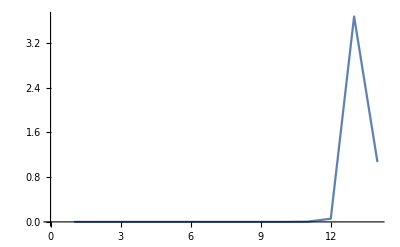

```mathematica
tt=Table[Max[Flatten[(Inverse[hm[n]]-Inverse[N[hm[n]]])/Inverse[hm[n]]]],{n,1,14}]
ListPlot[tt,Joined->True,PlotRange->All]
```

In short, if we try to invert a Hilbert matrix of order much larger than ten, the results we get are no more than numerical noise.

### Orthogonal Functions

There are many families of functions with the orthogonality property which makes the expansion of an arbitrary function easy. The best known are the trigonometric functions, which form the basis of Fourier series. We know that these functions form an orthogonal set, as we can check for functions defined over the interval [0,L]

```mathematica
rr={Sin[ 2(m+n)π]->0,Sin[2  (m-n) π]->0,Cos[2 (m+n)π]->1,Cos[2 (m-n) π]->1,Sin[a_Integer n π]->0,Cos[a_Integer?EvenQ n π]->1}
sinsin=∫_0^L Sin[2 m π x/L] Sin[2 n π x/L]ⅆx;
sinsin/.rr
Limit[sinsin,m->n]/.rr
sincos=∫_0^L Sin[2m π x/L] Cos[2n π x/L]ⅆx;
sincos/.rr
Limit[sincos,m->n]/.rr
coscos=∫_0^L Cos[2m π x/L] Cos[2n π x/L]ⅆx;
coscos/.rr
Limit[coscos,m->n]/.rr
```

{Sin[2 (m+n) π]→0,Sin[2 (m-n) π]→0,Cos[2 (m+n) π]→1,Cos[2 (m-n) π]→1,Sin[n π a_Integer]→0,Cos[n π a_Integer?EvenQ]→1}

0

L/2

0

0

0

L/2

So expanding a function into a series of trigonometric functions is very straightforward. In fact it is done so frequently that Mathematica has built-in functions to do it.

First, let's look at a nice smooth periodic function with period 1.

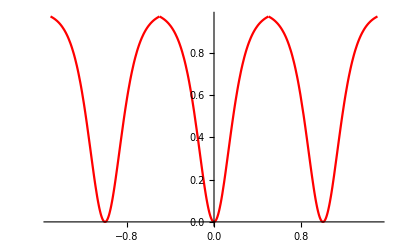

```mathematica
smooth=Plot[Tanh[5(t-Round[t])]^2,{t,-1.5,1.5},PlotStyle->{RGBColor[1,0,0]}]
```

The function FourierTrigSeries assumes that the function being expanded is periodic, and we want the interval between -1/2 and 1/2 to be repeated, so it is just the function Thanh[5t]^2 that we need to provide to FourierTrigSeries. We do need to alter the default period, though, using the option FourierParameters. Start by forming the first three terms.

```mathematica
smexp[n_]:=FourierTrigSeries[Tanh[5t]^2,t,n,FourierParameters-> {1,2π}]
sm3=smexp[3];
```

The coefficients in the transform are pretty messy,  but at least Mathematica  is smart enough to simplify the coefficients of the Sin terms to zero (as they must be, as this is an even function).

Still, even with just three terms in the expansion we get a good representation of the original function.

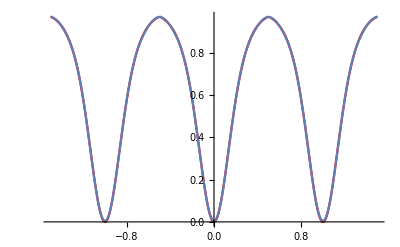

```mathematica
Show[smooth,Plot[Evaluate[sm3],{t,-1.5,1.5}]]
```

Functions with discontinuities are not as easy. We will try to form the Fourier series that describes a saw-tooth function.

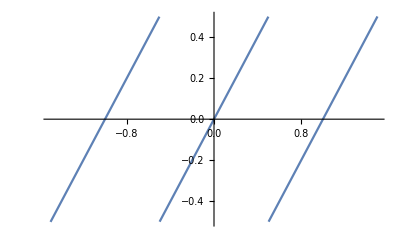

```mathematica
sawtooth=Plot[t-Round[t],{t,-1.5,1.5}]
```

Again as FourierTrigSeries assumes that the function being expanded is periodic, it is just the function f(t)=t that we need to provide to FourierTrigSeries.

```mathematica
sawexp[n_]:=FourierTrigSeries[t,t,n,FourierParameters-> {1,2π}]
sawexp[3]
```

Sin[2 π t]/π-Sin[4 π t]/(2 π)+Sin[6 π t]/(3 π)

Again Mathematica spots the symmetry: as t is an odd function, we should not be surprised that our expansion contains only odd functions, that is, sine functions. 

Now we'll see how taking 1, 4, 7 or 10 terms in the series improve our approximation to the original function.

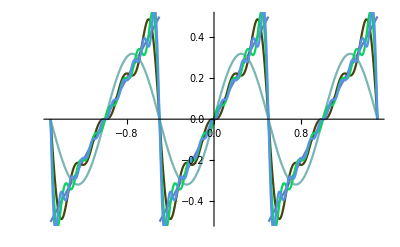

```mathematica
sawtab=Table[sawexp[n],{n,1,10,3}];
Show[sawtooth,Plot[Evaluate[sawtab],{t,-1.5,1.5},PlotStyle->Table[{RGBColor[RandomReal[],RandomReal[],RandomReal[]]},{n,1,10,3}]]]
```

What we see is that the Fourier series never quite gets to the saw-tooth function. A bit more experimentation shows that as we increase the number of terms we get a better and better approximation to more and more of the sloping line, but that there is always a deviation near the ends of the slope. This is a consequence of the presence of the step discontinuity in the saw-tooth function. Perhaps we should not be surprised that a sum of smooth functions cannot replicate a discontinuous function.
      
What happens as we add more terms is that we get higher, but narrower, 'overshoot' regions at the ends of the slope. This is quite a general behaviour for discontinuous functions (you might like to experiment with a square wave), and is known as the Gibbs phenomenon.

Fourier series often form a systematic way of solving differential equations. If the general solutions can be expressed in terms of sines and cosines, then particular solutions can be formed by linear superposition of these trigonometric functions.

### Fourier Transforms

The Fourier series we have just been looking at have been applied to periodic functions, with a finite period. For example, if the period is L then we have a series in sines and cosines of 2n π x/L.  In the limit as L→ ∞ the spacing between the different values of the wave vector, 2 π/L, tends to zero, and we can regard the wave vector as a continuous variable.  Then the summation in the Fourier series becomes an integral, and we have a Fourier transform.

Note that Mathematica has a built-in function which may or may not be more efficient than writing out the integral -- but at least it contains the relevant arbitrary constants.

```mathematica
ee[α_,x_]:=Exp[-α x^2]
Timing[ff[α_,k_]=Integrate[ee[α,x] Exp[I k x],{x,-∞,∞}]]
```

{4.56202,ConditionalExpression[(ⅇ^(-k^2/(4 α)) √π)/(√α),Re[α]>0]}

```mathematica
Timing[ff[α_,k_]=FourierTransform[ee[α,x],x,k]]
```

{0.00885,(ⅇ^(-k^2/(4 α)))/(√2 √α)}

The inverse function works as it should

```mathematica
Simplify[InverseFourierTransform[ff[α,k],k,x]-ee[α,x],α>0]
```

0

It is interesting to see how a range of functions of different widths transform. Generate the list of functions.

```mathematica
ll[x_]=Thread[ee[{.1,1,10},x]]
```

{ⅇ^(-0.1 x^2),ⅇ^(-x^2),ⅇ^(-10 x^2)}

```mathematica
mm[k_]=FourierTransform[ll[x],x,k]
```

{2.23607 ⅇ^(-2.5 k^2),(ⅇ^(-k^2/4))/(√2),(ⅇ^(-k^2/40))/(2 √5)}

Define a plotting style to give each of the three graphs a different colour (or color -- despite Stephen Wolfram's thoroughly British education at Oxford's Dragon School, his brainchild Mathematica uses United States spelling)

```mathematica
sty={{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0,0,1]}}
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

Use GraphicsArray to plot the two graphs side-by-side

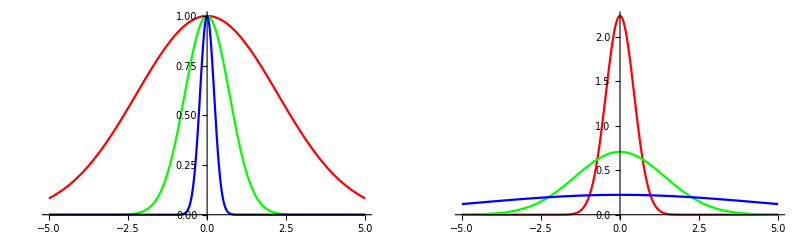

```mathematica
Show[GraphicsRow[{Plot[Evaluate[ll[x]],{x,-5,5},PlotStyle->sty,PlotRange->All],Plot[Evaluate[mm[x]],{x,-5,5},PlotStyle->sty,PlotRange->All]}]]
```

This presents a universal truth -- the more widely spread the original function, the more compact the Fourier transform.  This links to the uncertainty principle in quantum mechanics.  The wave vector k in the Fourier transform is proportional to the momentum, so we see that the more closely confined a particle is in real space (as represented by a narrow wave function) the less certainty there is about its momentum.

### Fourier Transforms and Differential Equations

One particularly useful feature of Fourier transforms is the way in which they affect derivatives. For example,

```mathematica
FourierTransform[D[f[x],x],x,k]
FourierTransform[f'[x],x,k]
```

-ⅈ k FourierTransform[f[x],x,k]

-ⅈ k FourierTransform[f[x],x,k]

so that a differential equation can be transformed, by a Fourier transform, into an algebraic equation. As an example, consider the forced harmonic oscillator

```mathematica
eqf=x''[t]+ω0^2 x[t]==a Cos[ωf t]
```

ω0^2 x[t]+x''[t]==a Cos[t ωf]

Fourier transform the equation by Threading the transformation through both sides of the equation.

```mathematica
eqft=Thread[FourierTransform[#,t,ω]&[eqf],Equal]
```

FourierTransform[ω0^2 x[t]+x''[t],t,ω]==a √(π/2) DiracDelta[ω-ωf]+a √(π/2) DiracDelta[ω+ωf]

Unfortunately, Mathematica needs to be told a few things about the Fourier transform -- essentially, the fact that it is a linear operation.

```mathematica
FourierTransform[ω0^2 x[t]+x''[t],t,ω]==a √(π/2) DiracDelta[ω-ωf]+a √(π/2) DiracDelta[ω+ωf]
```

FourierTransform[ω0^2 x[t]+x''[t],t,ω]==a √(π/2) DiracDelta[ω-ωf]+a √(π/2) DiracDelta[ω+ωf]

```mathematica
eqft/.FourierTransform[a_+b_,c_,d_]:>FourierTransform[a,c,d]+FourierTransform[b,c,d]/.FourierTransform[a_ f_[t],c_,d_]:>a FourierTransform[f[t],c,d]
```

-ω^2 FourierTransform[x[t],t,ω]+ω0^2 FourierTransform[x[t],t,ω]==a √(π/2) DiracDelta[ω-ωf]+a √(π/2) DiracDelta[ω+ωf]

```mathematica
%/.FourierTransform[x[t],t,ω]->xf[ω]
```

-ω^2 xf[ω]+ω0^2 xf[ω]==a √(π/2) DiracDelta[ω-ωf]+a √(π/2) DiracDelta[ω+ωf]

```mathematica
ss=Solve[%,xf[ω]]
```

{{xf[ω]→(-a √(2 π) DiracDelta[ω-ωf]-a √(2 π) DiracDelta[ω+ωf])/(2 (ω^2-ω0^2))}}

```mathematica
fxsol[ω_]=xf[ω]/.ss[[1,1]]
```

(-a √(2 π) DiracDelta[ω-ωf]-a √(2 π) DiracDelta[ω+ωf])/(2 (ω^2-ω0^2))

```mathematica
xsol[t_]=InverseFourierTransform[fxsol[ω],ω,t]//ExpToTrig
```

(a Cos[t ωf])/(ω0^2-ωf^2)

This reproduces the resonant singular behaviour  of the forced harmonic oscillator we are familiar with when the forcing frequency ωf is equal to the resonant frequency ω0.

### Fourier methods in data smoothing

As well as Fourier series and transforms which work with analytic functions, there are methods for finding Fourier transforms of purely numerical data. These work very efficiently, and are often used embedded within numerical methods for solving problems. 
One frequently finds data contaminated with noise, and can see by inspection of a graph that the noise is of a higher frequency than the underlying data. Fourier methods can be used to reduce the noise content. This might be a good point at which to look back to the PHAS1449 course, to remind yourself about how data can be read into Mathematica from external files, but here we will construct artificial data. Consider the following set of data, generated as the sum of two sinusoidal waves with random noise.

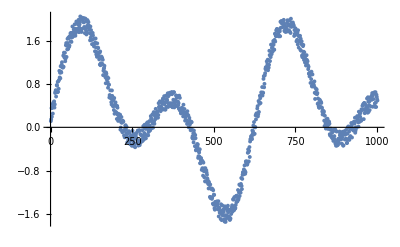

```mathematica
sinda=Table[Sin[x]+Sin[2 x]+0.3 RandomReal[],{x,0,10,0.01}];
ListPlot[sinda]
```

We can do a numerical Fourier transform of the data

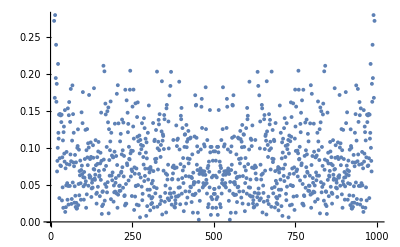

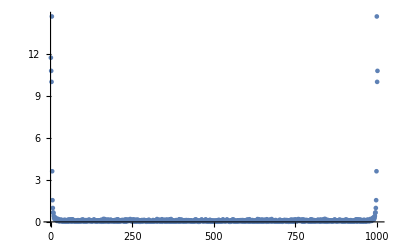

```mathematica
tr=Fourier[sinda];
ListPlot[Abs[tr]]
ListPlot[Abs[tr],PlotRange->All]
```

The Fourier function returns a list which runs Δω{0,1,2,...,high frequency,-high frequency,...,-2,-1} and so we can see from this graph that there is a small high-frequency background.  This suggests that we try losing the parts of the transform that are less than, say, 0.25, then transforming back (with a final Chop to remove any small imaginary part from the inverse transform).

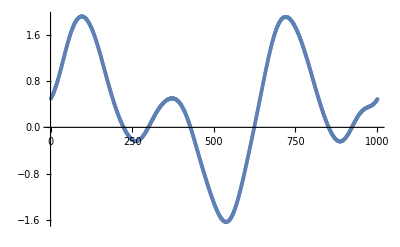

```mathematica
itr=Chop[InverseFourier[Chop[tr,0.25]],0.001];
ListPlot[itr]
```

The resulting trace is significantly clearer.

## Summary

This lecture started with a very general problem of series expansions of functions, and then specialised that to Fourier series (where a function is defined on a finite range, but is then imagined to be periodically repeated and is then expanded in terms of sines and cosines, or complex exponentials). The next problem was that of a function defined on an infinite interval, when the summation is replaced by an integral. We have seen how Fourier transforms may be applied in solving differential equations and in smoothing data -- just two examples form the enormous range of applications.

A.H. Harker
Physics and Astronomy, UCL
September 2005; 
revised for Mathematica version 5.2 March 2007; 
further revised February 2008;
revised for Mathematica version 6.0 March 2009
revised for Mathematica version 7.0 March 2010.
Amended by Patrick Guio, Physics and Astronomy, UCL, March 2014, March 2015, March 2016, March 2017.